## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW170608";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
raw=Import[FileNameJoin[{baseDir,eventID,"GR"<>"_IMRP_posterior.csv"}]];
samples["GR"]=(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]](*spin2z*)};
```

## m1-m2 Plot, 22

```mathematica
plots=<||>;
compPlots=<||>;
evolPlots=<||>
vsPlots=<||>;
vsPlots["p2p4"]={};
```

<||>

## Compute GR m1 and m2 PDF

```mathematica
p="GR"
m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

maxPoint=NMaximize[{m1m2PDF["GR"][x,y],5<x<20&&5<y<20},{x,y}]
m1m2Max=Reverse[Values[maxPoint[[2]]]]
```

GR

输入Mc范围：{3,40}

输入q范围：{1,3}

m1范围：{3.4461,81.9069}

m2范围：{2.04767,45.9479}

对称数据：原始 22641 + 镜像 22641

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

{0.0963773,{x→8.59887,y→9.842}}

{9.842,8.59887}

```mathematica
samples["GR"]
```

Missing[KeyAbsent,GR]

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文_v01\\paper\\submit_final",""}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];
```

```mathematica
(*Export[FileNameJoin[{targetDir,"xxx.pdf"}],evoPlots2[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->80/25.4*72]*)
```

## 5l,4,6,2,7 6 5l,6 4,5l,6 2,4,5l,6 2,4,5l,6,7

```mathematica
evoPlots1=<||>
evoPlots2=<||>
evoPlots3=<||>
evoPlots4=<||>
evoPlots5=<||>
```

<||>

## Compute GR m1 and m2 PDF

### fig1, abcd

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
CASE="p6_init";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0702};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0702}，共 2 条

第一条前3点：{{9.48235,9.23288},{9.48239,9.23283},{9.54992,9.16949}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.227086

可信水平百分比：22.7086%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7} 预处理完成，红线包含概率 prob = 0.227086

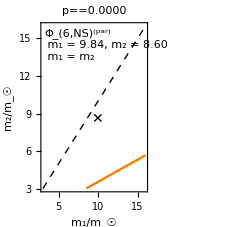

```mathematica
CASE="p6_init";
p={"dphi_6"};
probability=0.0000;
(*probability=0.2;*)

evoPlots1[CASE]=PlotMultiInversionWithMode[p,{probability},3,16,0.02,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"NONE",(*Points模式下关闭填充，避免无效计算*)mode->{"Points"},extremePointsList->{{m1m2Max}},extremePointsMarkerList->{"Cross"},extremePointsLegendList->{Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,maskM1ltM2->False,debugHatch->False        (*关闭调试输出，保持干净*)]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig1a.pdf"}],evoPlots1[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig1a.pdf

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
CASE="p6_before";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.077};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.077}，共 2 条

第一条前3点：{{9.44221,9.19265},{9.4837,9.15362},{9.48837,9.14925}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.173028

可信水平百分比：17.3028%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.173028

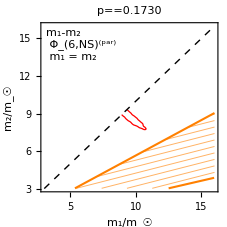

```mathematica
CASE="p6_before";
p={"dphi_6"};
probability=prob;
(*probability=0.0000;*)
(*probability=0.2;*)

evoPlots1[CASE]=PlotMultiInversionWithMode[p,{probability},3,16,0.02,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,mode->{"Boundary"},extremePointsList->{{m1m2Max}},extremePointsMarkerList->{"Cross"},extremePointsLegendList->{"Max/Min of α₅ₗ"},showVerificationStats->False,debugHatch->False]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig1b.pdf"}],evoPlots1[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig1b.pdf

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
CASE="p6_at";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0702};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0702}，共 2 条

第一条前3点：{{9.48235,9.23288},{9.48239,9.23283},{9.54992,9.16949}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.227086

可信水平百分比：22.7086%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.227086

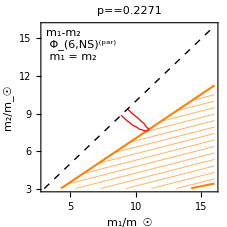

```mathematica
CASE="p6_at";
p={"dphi_6"};
probability=prob;
(*probability=0.0000;*)
(*probability=0.2;*)

evoPlots1[CASE]=PlotMultiInversionWithMode[p,{probability},3,16,0.02,cm->True,cd->{0},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,mode->{"Boundary"},extremePointsList->{{m1m2Max}},extremePointsMarkerList->{"Cross"},extremePointsLegendList->{"Max/Min of α₅ₗ"},showVerificationStats->False,debugHatch->False]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig1c.pdf"}],evoPlots1[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig1c.pdf

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
CASE="p6_after";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.066};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.066}，共 2 条

第一条前3点：{{9.50691,9.25776},{9.50711,9.25755},{9.54664,9.22047}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.260699

可信水平百分比：26.0699%

==========================

{dphi_2,dphi_6} 预处理完成，红线包含概率 prob = 0.260699

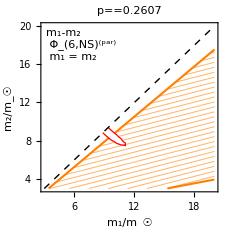

```mathematica
CASE="p6_after";
p={"dphi_6"};
probability=prob;
(*probability=0.0000;*)
(*probability=0.2;*)

evoPlots1[CASE]=PlotMultiInversionWithMode[p,{probability},3,20,0.02,cm->True,cd->{0},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,mode->{"Boundary"},extremePointsList->{{m1m2Max}},extremePointsMarkerList->{"Cross"},extremePointsLegendList->{"Max/Min of α₅ₗ"},showVerificationStats->False,debugHatch->False]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig1d.pdf"}],evoPlots1[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig1d.pdf

### fig2, abcd

```mathematica
CASE="p26_init";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.066};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.066}，共 2 条

第一条前3点：{{9.50691,9.25776},{9.50711,9.25755},{9.54664,9.22047}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.260699

可信水平百分比：26.0699%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.260699

警告：参数 dphi_2 模式为 Points，但未提供有效 extremePointsList，已跳过。

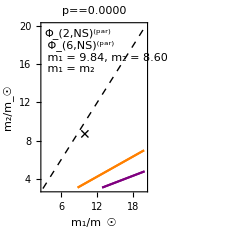

```mathematica
CASE="p26_init";
p={"dphi_2","dphi_6"};
probability=0.0000;
(*probability=0.2;*)

evoPlots2[CASE]=PlotMultiInversionWithMode[p,{probability,probability},3,20,0.1,cm->True,cd->{1,1},cu->{1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"NONE",mode->{"Points","Points"},extremePointsList->{{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross"},extremePointsLegendList->{"",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,debugHatch->False]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig2a.pdf"}],evoPlots2[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig2a.pdf

```mathematica
CASE="p26_before";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.075};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.075}，共 2 条

第一条前3点：{{9.45404,9.20448},{9.48057,9.17952},{9.51286,9.14925}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.190017

可信水平百分比：19.0017%

==========================

{dphi_2,dphi_6} 预处理完成，红线包含概率 prob = 0.190017

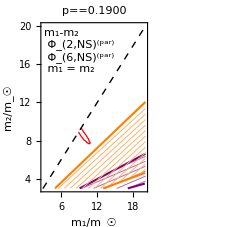

```mathematica
CASE="p26_before";
p={"dphi_2","dphi_6"};
probability=prob;
(*probability=0.2;*)

evoPlots2[CASE]=PlotMultiInversionWithMode[p,{probability,probability},3,20,0.02,cm->True,cd->{1,1},cu->{1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,mode->{"Boundary","Boundary"},extremePointsList->{{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross"},extremePointsLegendList->{"Max/Min of α₅ₗ","Max/Min of α₅ₗ"},showVerificationStats->False,debugHatch->False,layerOrder->{1,2}]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig2b.pdf"}],evoPlots2[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig2b.pdf

```mathematica
CASE="p26_at6";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0702};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0702}，共 2 条

第一条前3点：{{9.48235,9.23288},{9.48239,9.23283},{9.54992,9.16949}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.227086

可信水平百分比：22.7086%

==========================

{dphi_2,dphi_6} 预处理完成，红线包含概率 prob = 0.227086

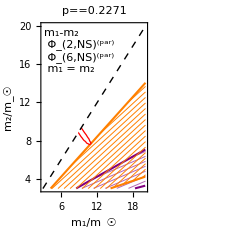

```mathematica
CASE="p26_at6";
p={"dphi_2","dphi_6"};
probability=prob;
(*probability=0.2;*)

evoPlots2[CASE]=PlotMultiInversionWithMode[p,{probability,probability},3,20,0.02,cm->True,cd->{1,0},cu->{1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,mode->{"Boundary","Boundary"},extremePointsList->{{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross"},extremePointsLegendList->{"Max/Min of α₅ₗ","Max/Min of α₅ₗ"},showVerificationStats->False,opaqueIndices->{2},debugHatch->False,layerOrder->{1,2}]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig2c.pdf"}],evoPlots2[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig2c.pdf

```mathematica
CASE="p26_at2";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0499};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0499}，共 2 条

第一条前3点：{{8.61986,8.86942},{8.61602,8.87283},{8.54628,8.93959}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.423768

可信水平百分比：42.3768%

==========================

{dphi_2,dphi_6} 预处理完成，红线包含概率 prob = 0.423768

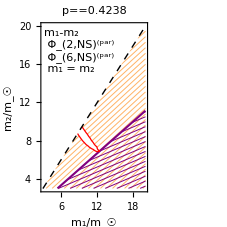

```mathematica
CASE="p26_at2";
p={"dphi_2","dphi_6"};
probability=prob;
(*probability=0.2;*)

evoPlots2[CASE]=PlotMultiInversionWithMode[p,{probability,probability},3,20,0.02,cm->True,cd->{1,0},cu->{1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],lineStyles->{Automatic,{Directive[Opacity[0.0]],Automatic}},fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,mode->{"Boundary","Boundary"},extremePointsList->{{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross"},extremePointsLegendList->{"Max/Min of α₅ₗ","Max/Min of α₅ₗ"},showVerificationStats->False,opaqueIndices->{1},debugHatch->False,layerOrder->{2,1}]
```

```mathematica
ClearAll[layerOrder];
Remove[layerOrder];
```

```mathematica
Export[FileNameJoin[{targetDir,"fig2d.pdf"}],evoPlots2[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig2d.pdf

### fig3, abcd

Part::partw: Part 2 of contourPoints[p246_init] does not exist.

警告：参数 dphi_2 模式为 Points，但未提供有效 extremePointsList，已跳过。

警告：参数 dphi_4 模式为 Points，但未提供有效 extremePointsList，已跳过。

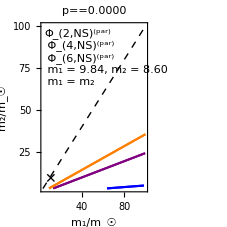

```mathematica
CASE="p246_init";
p={"dphi_2","dphi_4","dphi_6"};
probability=0.0000;
(*probability=0.2;*)

evoPlots3[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability},3,100,0.1,cm->True,cd->{1,1,1},cu->{1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"NONE",mode->{"Points","Points","Points"},extremePointsList->{{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross"},extremePointsLegendList->{"","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,debugHatch->False]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig3a.pdf"}],evoPlots3[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig3a.pdf

```mathematica
CASE="p246_before";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.076};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.076}，共 2 条

第一条前3点：{{9.44813,9.19857},{9.48213,9.16657},{9.50061,9.14925}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.181804

可信水平百分比：18.1804%

==========================

{dphi_2,dphi_4,dphi_6} 预处理完成，红线包含概率 prob = 0.181804

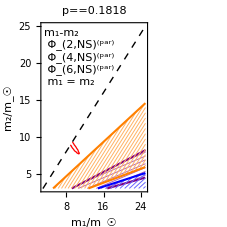

```mathematica
CASE="p246_before";
p={"dphi_2","dphi_4","dphi_6"};
probability=prob;
(*probability=0.2;*)

evoPlots3[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability},3,25,0.02,cm->True,cd->{1,1,1},cu->{1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,mode->{"Boundary","Boundary","Boundary"},extremePointsList->{{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross"},extremePointsLegendList->{"","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,debugHatch->False,layerOrder->{1,2,3}]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig3b.pdf"}],evoPlots3[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig3b.pdf

```mathematica
CASE="p246_at6";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0702};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0702}，共 2 条

第一条前3点：{{9.48235,9.23288},{9.48239,9.23283},{9.54992,9.16949}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.227086

可信水平百分比：22.7086%

==========================

{dphi_2,dphi_4,dphi_6} 预处理完成，红线包含概率 prob = 0.227086

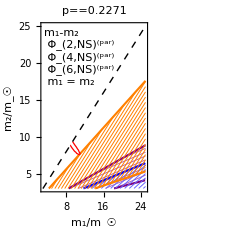

```mathematica
CASE="p246_at6";
p={"dphi_2","dphi_4","dphi_6"};
probability=prob;
(*probability=0.2;*)

evoPlots3[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability},3,25,0.02,cm->True,cd->{1,1,0},cu->{1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,mode->{"Boundary","Boundary","Boundary"},extremePointsList->{{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross"},extremePointsLegendList->{"","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,opaqueIndices->{3},debugHatch->False,layerOrder->{1,2,3}]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig3c.pdf"}],evoPlots3[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig3c.pdf

```mathematica
CASE="p246_at2";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0499};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0499}，共 2 条

第一条前3点：{{8.61986,8.86942},{8.61602,8.87283},{8.54628,8.93959}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.423768

可信水平百分比：42.3768%

==========================

{dphi_2,dphi_4,dphi_6} 预处理完成，红线包含概率 prob = 0.423768

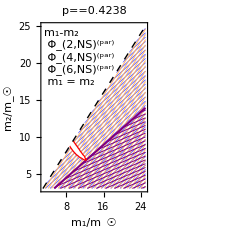

```mathematica
CASE="p246_at2";
p={"dphi_2","dphi_4","dphi_6"};
probability=prob;
(*probability=0.2;*)

evoPlots3[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability},3,25,0.02,cm->True,cd->{1,1,0},cu->{1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,lineStyles->{Automatic,{Directive[Opacity[0.0]],Directive[Opacity[0.0]]},{Directive[Opacity[0.0]],Directive[Opacity[0.0]]}},mode->{"Boundary","Boundary","Boundary"},extremePointsList->{{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross"},extremePointsLegendList->{"","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,opaqueIndices->{1},debugHatch->False,layerOrder->{2,3,1}]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig3d.pdf"}],evoPlots3[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig3d.pdf

### fig4, abcd

Part::partw: Part 2 of contourPoints[p245l6_init] does not exist.

警告：参数 dphi_2 模式为 Points，但未提供有效 extremePointsList，已跳过。

警告：参数 dphi_4 模式为 Points，但未提供有效 extremePointsList，已跳过。

警告：参数 dphi_5l 模式为 Points，但未提供有效 extremePointsList，已跳过。

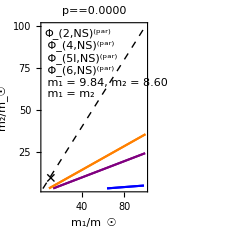

```mathematica
CASE="p245l6_init";
p={"dphi_2","dphi_4","dphi_5l","dphi_6"};
probability=0.0000;
(*probability=0.2;*)

evoPlots4[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability},3,100,0.1,cm->True,cd->{1,1,1,1},cu->{1,1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"NONE",hatchSpacing->0.5,hatchThickness->0.7,mode->{"Points","Points","Points","Points"},extremePointsList->{{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,debugHatch->False]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig4a.pdf"}],evoPlots4[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig4a.pdf

```mathematica
CASE="p245l6_see5l";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.074};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.074}，共 2 条

第一条前3点：{{9.01154,8.76242},{9.01284,8.76328},{9.02645,8.75402}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.197917

可信水平百分比：19.7917%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6} 预处理完成，红线包含概率 prob = 0.197917

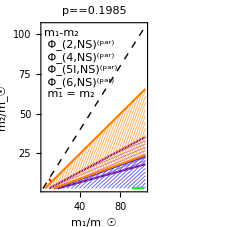

```mathematica
CASE="p245l6_see5l";
p={"dphi_2","dphi_4","dphi_5l","dphi_6"};
probability=prob;
probability=0.1985;

evoPlots4[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability},3,105,0.1,cm->True,cd->{1,1,1,1},cu->{1,1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->2,hatchThickness->0.7,mode->{"Boundary","Boundary","Boundary","Boundary"},extremePointsList->{{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,debugHatch->False]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig4b.pdf"}],evoPlots4[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig4b.pdf

```mathematica
CASE="p245l6_at4";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0553};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0553}，共 2 条

第一条前3点：{{9.32034,9.5699},{9.28847,9.60387},{9.21261,9.68522}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.363336

可信水平百分比：36.3336%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6} 预处理完成，红线包含概率 prob = 0.363336

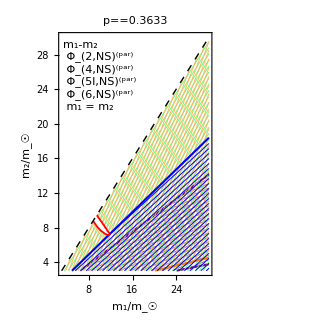

```mathematica
CASE="p245l6_at4";
p={"dphi_2","dphi_4","dphi_5l","dphi_6"};
probability=prob;
(*probability=0.2;*)

evoPlots4[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability},3,30,0.02,cm->True,cd->{1,1,0,0},cu->{1,0,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,lineStyles->{Automatic,{Automatic,Automatic},{Directive[Opacity[0.0]],Directive[Opacity[0.0]]},{Directive[Opacity[0.0]],Automatic}},mode->{"Boundary","Boundary","Boundary","Boundary"},extremePointsList->{{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,opaqueIndices->{2},debugHatch->False,layerOrder->{1,3,4,2}]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig4c.pdf"}],evoPlots4[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig4c.pdf

```mathematica
CASE="p245l6_at2";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0499};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0499}，共 2 条

第一条前3点：{{8.61986,8.86942},{8.61602,8.87283},{8.54628,8.93959}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.423768

可信水平百分比：42.3768%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6} 预处理完成，红线包含概率 prob = 0.423768

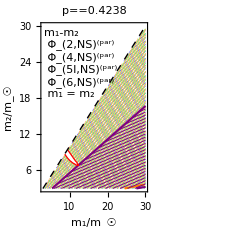

```mathematica
CASE="p245l6_at2";
p={"dphi_2","dphi_4","dphi_5l","dphi_6"};
probability=prob;
(*probability=0.2;*)

evoPlots4[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability},3,30,0.02,cm->True,cd->{1,1,0,0},cu->{1,0,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,lineStyles->{Automatic,{Directive[Opacity[0.0]],Directive[Opacity[0.0]]},{Directive[Opacity[0.0]],Automatic},{Directive[Opacity[0.0]],Automatic}},mode->{"Boundary","Boundary","Boundary","Boundary"},extremePointsList->{{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,opaqueIndices->{1},debugHatch->False,layerOrder->{2,3,4,1}]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig4d.pdf"}],evoPlots4[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig4d.pdf

### fig5, abcd

Part::partw: Part 2 of contourPoints[p245l67_init] does not exist.

警告：参数 dphi_2 模式为 Points，但未提供有效 extremePointsList，已跳过。

警告：参数 dphi_4 模式为 Points，但未提供有效 extremePointsList，已跳过。

警告：参数 dphi_5l 模式为 Points，但未提供有效 extremePointsList，已跳过。

警告：参数 dphi_6 模式为 Points，但未提供有效 extremePointsList，已跳过。

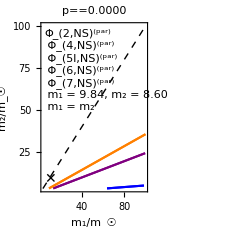

```mathematica
CASE="p245l67_init";
p={"dphi_2","dphi_4","dphi_5l","dphi_6","dphi_7"};
probability=0.0000;
(*probability=0.2;*)

evoPlots5[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability,probability},3,100,0.1,cm->True,cd->{1,1,1,1,1},cu->{1,1,1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"NONE",hatchSpacing->0.5,hatchThickness->0.7,lineStyles->{{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Directive[Opacity[0.0]],Directive[Opacity[0.0]]}},mode->{"Points","Points","Points","Points","Points"},extremePointsList->{{},{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,debugHatch->False]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig5a.pdf"}],evoPlots5[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig5a.pdf

```mathematica
CASE="p245l67_at7";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.079};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.079}，共 2 条

第一条前3点：{{8.80231,9.05187},{8.78399,9.08156},{8.78077,9.08662}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.148209

可信水平百分比：14.8209%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7} 预处理完成，红线包含概率 prob = 0.148209

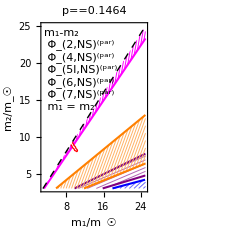

```mathematica
CASE="p245l67_before";
p={"dphi_2","dphi_4","dphi_5l","dphi_6","dphi_7"};
probability=prob;
probability=0.1464;

evoPlots5[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability,probability},3,25,0.02,cm->True,cd->{1,1,1,1,0},cu->{1,1,1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,lineStyles->{{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Automatic,Directive[Opacity[0.0]]}},mode->{"Boundary","Boundary","Boundary","Boundary","Boundary"},extremePointsList->{{},{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,opaqueIndices->{5},debugHatch->False]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig5b.pdf"}],evoPlots5[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig5b.pdf

```mathematica
CASE="p245l67_at5l";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.063699};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.063699}，共 2 条

第一条前3点：{{9.52037,9.2714},{9.52065,9.27109},{9.54485,9.2484}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.285612

可信水平百分比：28.5612%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7} 预处理完成，红线包含概率 prob = 0.285612

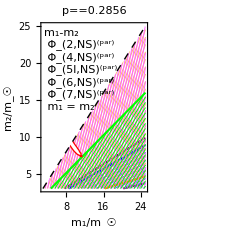

```mathematica
CASE="p245l67_at5l";
p={"dphi_2","dphi_4","dphi_5l","dphi_6","dphi_7"};
probability=prob;
(*probability=0.1464;*)

evoPlots5[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability,probability},3,25,0.02,cm->True,cd->{1,1,0,0,1},cu->{1,1,1,1,0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,lineStyles->{{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Directive[Opacity[0.0]],Automatic},{Automatic,Directive[Opacity[0.0]]}},mode->{"Boundary","Boundary","Boundary","Boundary","Boundary"},extremePointsList->{{},{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,opaqueIndices->{3},debugHatch->False,layerOrder->{1,2,4,5,3}]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig5c.pdf"}],evoPlots5[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig5c.pdf

```mathematica
CASE="p245l67_at2";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0499};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0499}，共 2 条

第一条前3点：{{8.61986,8.86942},{8.61602,8.87283},{8.54628,8.93959}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.423768

可信水平百分比：42.3768%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7} 预处理完成，红线包含概率 prob = 0.423768

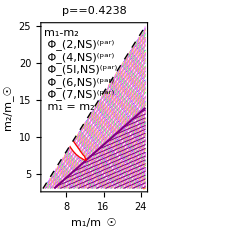

```mathematica
CASE="p245l67_at2";
p={"dphi_2","dphi_4","dphi_5l","dphi_6","dphi_7"};
probability=prob;
(*probability=0.1464;*)

evoPlots5[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability,probability},3,25,0.02,cm->True,cd->{1,1,0,0,1},cu->{1,0,1,1,0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],fillStyle->"hatch",hatchSpacing->0.5,hatchThickness->0.7,lineStyles->{{Automatic,Automatic},{Directive[Opacity[0.0]],Directive[Opacity[0.0]]},{Directive[Opacity[0.0]],Automatic},{Directive[Opacity[0.0]],Automatic},{Automatic,Directive[Opacity[0.0]]}},mode->{"Boundary","Boundary","Boundary","Boundary","Boundary"},extremePointsList->{{},{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,opaqueIndices->{1},debugHatch->False,layerOrder->{2,3,4,5,1}]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig5d.pdf"}],evoPlots5[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig5d.pdf